```mathematica
Clear[n,L,S]
```

```mathematica
n=120;
```

```mathematica
f[k_]:=If[k>=0,Fibonacci[k],0]
```

```mathematica
∑_(k=1)^(n-2) (f[k-1] f[n-k]+f[k] f[n-k-3])
```

```mathematica
z[L_,n_]:=∑_(k=1)^(n-2) (f[k-L+1] f[n-k]+∑_(l=2)^L f[k-L+l] f[n-l-k-1])
```

```mathematica
S[n_]:=∑_(k=1)^Floor[n/3] (-1)^(k+1) Binomial[n-2 k,k] k 2^(n-3 k)
```

```mathematica
P[n_]:=N[∑_(L=1)^(n-1) 1/L z[L,n]/S[n]]
```

```mathematica
P[10]
```

0.586991

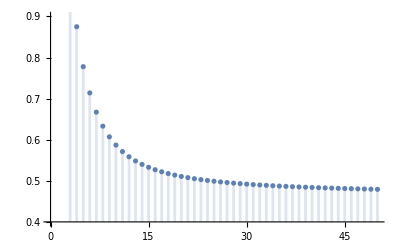

```mathematica
DiscretePlot[P[n],{n,3,50},PlotRange->{0.4,0.9}]
```